```mathematica
RowDelete[x_,entries_]:=Module[{list,i},
list=Table[{entries[[i]]},{i,1,Length[entries]}];
Delete[x,list]
]
(*ColumnDelete takes a matrix and delete the specified columns*)
ColumnDelete[x_,entries_]:=Module[{},
Transpose[RowDelete[Transpose[x],entries]]
]
(*AddZeroToRow adds a zero to a row vector*)
AddZeroToRow[x_,j_]:=Module[{l},
l=Length[x];
Join[Take[x,j-1],{0},Take[x,-(l-j+1)]]
]
(*AddZerosToRow will add any number of zeros to a row vector*)
AddZerosToRow[x_,entries_]:=Module[{y,list,i},
y=x;
list=Sort[entries];
For[i=1,i≤Length[list],i++,
y=AddZeroToRow[y,list[[i]]]
];
y
]


MAR[datasets_, cov_, constraints_]:=Module[{X,U,Y,Z,D,d0,p,x0,u0,y0,one,popdata,covdata,tanks,tankrow,index,tempdata,c,j,k},
p=Length[datasets[[1,1]]]-cov;

If[cov==0,
X={};Y={};
For[j=1,j≤Length[datasets],j++,
x0=Delete[datasets[[j]],Length[datasets[[j]]]];
y0=Delete[datasets[[j]],1];
X=Join[X,x0];
Y=Join[Y,y0]
];
one={Table[1,{i,1,Length[X]}]};
Z=Transpose[Join[one,Transpose[X]]];
D={};
For[k=1,k≤p,k++,
c={};
For[j=1,j≤p,j++,
c=Join[c,If[MemberQ[constraints,{k,j}],{j},{}]]
];
d0={AddZerosToRow[Flatten[{Y[[All,k]]}.ColumnDelete[Z,c+1].Inverse[Transpose[ColumnDelete[Z,c+1]].ColumnDelete[Z,c+1]]],c+1]};
D=Join[D,d0]
];
D,

X={};Y={};U={};
For[j=1,j≤Length[datasets],j++,
tempdata=datasets[[j]];
x0=tempdata[[All,cov+1;;cov+p]];
x0=Delete[x0,Length[x0]];
u0=tempdata[[All,1;;cov]];
u0=Delete[u0,Length[u0]];
y0=tempdata[[All,cov+1;;cov+p]];
y0=Delete[y0,1];

X=Join[X,x0];
U=Join[U,u0];
Y=Join[Y,y0];
];
one={Table[1,{i,1,Length[X]}]};
Z=Transpose[Join[one,Transpose[U],Transpose[X]]];
D={};
For[k=1,k≤p,k++,
c={};
For[j=1,j≤p,j++,
c=Join[c,If[MemberQ[constraints,{k,j}],{j},{}]]
];
d0={AddZerosToRow[Flatten[{Y[[All,k]]}.ColumnDelete[Z,c+1+cov].Inverse[Transpose[ColumnDelete[Z,c+1+cov]].ColumnDelete[Z,c+1+cov]]],c+1+cov]};
D=Join[D,d0]
];
D
]
]


ProcessData[raw_,cov_]:=Module[{rawdata,p,tankrow,tanks,purepopdata,logpopdata,covdata,processeddata,index,compdataset,i,i0,j,data},
rawdata=Delete[raw,1];
p=Length[rawdata[[1]]]-cov-1;

tankrow=Delete[raw[[All,1]],1];(*extracts the column of tank labels as a row vector.*)
tanks=DeleteDuplicates[tankrow];(*Just getting a list of tank labels*)

purepopdata=ColumnDelete[rawdata,{1}];
For[i=1,i≤cov,i++,
purepopdata=ColumnDelete[purepopdata,{1}]
];
logpopdata=Log[purepopdata];

If[cov==0,covdata={},
covdata=ColumnDelete[rawdata,{1}];
For[i=1,i≤p,i++,
covdata=ColumnDelete[covdata,{Length[covdata[[1]]]}]
]
];

processeddata=If[cov==0,Transpose[Join[{tankrow},Transpose[logpopdata]]],Transpose[Join[{tankrow},Transpose[covdata],Transpose[logpopdata]]]];(*Join log transformed values back up with tank labels*)

(*Below we extract tank specific processed data and label it by the tank label.*)
For[j=1,j≤Length[tanks],j++,
index=tanks[[j]];
data[index]={};
For[i=1,i≤Length[processeddata],i++,
i0=If[processeddata[[i,1]]==index,{processeddata[[i]]},{}];
data[index]=Join[data[index],i0]
];
data[index]=ColumnDelete[data[index],{1}]
];

compdataset={};
For[j=1,j≤Length[tanks],j++,
index=tanks[[j]];
compdataset=Join[compdataset,{data[index]}]
];
compdataset
]
```

```mathematica
SetDirectory["/Users/4/Documents/Weak interactions/tank data"];
rawdata[1]=Import["CER0.csv"];
rawdata[2]=Import["CER_DAP0.csv"];
rawdata[3]=Import["CER_SCA0.csv"];
rawdata[4]=Import["DAP0.csv"];
rawdata[5]=Import["DAPSCA0.csv"];
rawdata[6]=Import["SCA0.csv"];
rawdata[7]=Import["N0.csv"];
rawdata[8]=Import["N_CER0.csv"];
rawdata[9]=Import["N_CER_DAP0.csv"];
rawdata[10]=Import["N_CER_SCA0.csv"];
rawdata[11]=Import["N_DAP0.csv"];
rawdata[12]=Import["N_SCA0.csv"];
rawdata[13]=Import["N_SCA_DAP0.csv"];
rawdata[14]=Import["N_I_DAP0.csv"];
rawdata[15]=Import["N_I0.csv"];
rawdata[16]=Import["N_I_COP0.csv"];
rawdata[17]=Import["CER_SCA_DAP0.csv"];

(*1 covariate*)
rawdata[18]=Import["CER.csv"];
rawdata[19]=Import["CER_DAP.csv"];
rawdata[20]=Import["CER_SCA.csv"];
rawdata[21]=Import["DAP.csv"];
rawdata[22]=Import["DAPSCA.csv"];
rawdata[23]=Import["SCA.csv"];
rawdata[24]=Import["N.csv"];
rawdata[25]=Import["N_CER.csv"];
rawdata[26]=Import["N_CER_DAP.csv"];
rawdata[27]=Import["N_CER_SCA.csv"];
rawdata[28]=Import["N_Dap.csv"];
rawdata[29]=Import["N_Sca.csv"];
rawdata[30]=Import["N_SCA_DAP.csv"];
rawdata[31]=Import["N_I_DAP.csv"];

(*2 covariates*)
rawdata[32]=Import["N_I.csv"];
rawdata[33]=Import["N_I_cop.csv"];

For[i=1,i≤17,i++,
prodata[i]=ProcessData[rawdata[i],0];
m[i]=MAR[prodata[i],0,{}]
]
For[i=18,i≤33,i++,
prodata[i] = ProcessData[rawdata[i],1];
m[i]=MAR[prodata[i],1,{}]
]

MM={};
For[i=1,i≤17,i++,
tanks=Length[prodata[i]];
MM=Join[MM,{Table[MAR[{prodata[i][[j]]},0,{}],{j,1,tanks}]}]
]
```

```mathematica
(*Find distribution of B matrices (for off-diagonal and on-diagonal) and produce some new B matrices to use as "known" B matrices*)
(*Find covariance matrix of Sigma for the data and use that to produce noise*)
(*Refer to picture on your phone*)
(*Actual data took 26 samples from 6 tanks*)
(*Standard deviation for estimated B matrix should be smaller than known B matrix and tests for stability should be the similar if good estimate*)
```

```mathematica
B[D_]:=Module[{p,cov,B},(*extract B matrix*)
p=Length[D];
cov=Length[D[[1]]]-p-1;
B=D[[All,2+cov;;1+cov+p]]
]
```

```mathematica
For[i=1,i≤33,i++,
p=Length[m[i]];
cov=Length[m[i][[1]]]-p-1;
(*Amatrix[i] = m[i][[All,1;;1]];*)
Bmatrix[i] = B[m[i]];
(*If[cov == 0,
Cmatrix[i] = 0,
Cmatrix[i] = m[i][[All,2;;2+cov-1]]]*)
]
```

```mathematica
maxt = 50;
X[0] = {0,1,2};
For[t=1,t≤maxt,t++,
X[t] = Amatrix[1] + Bmatrix[1].X[t-1];
]
X[1]
```

{{1.76256},{1.39364},{-0.323391}}

```mathematica
nstr = 0.000001;
For[i=1,i≤17,i++,
Sigma[i]=IdentityMatrix[Length[prodata[i][[1]]]];
For[j=1,j≤Length[prodata[i][[1]]],j++,
For[k=1,k≤j,k++,
Sigma[i][[j,k]]=RandomReal[{-1,1}];
Sigma[i][[k,j]]=Sigma[i][[k,j]]
];
E[i]=RandomReal[{-nstr,nstr},{Length[prodata[i][[1]]]}];
Xlist[i] = {};
For[j=1,j≤ Length[prodata[i]],j++,
prep2 = {};
X[0] = prodata[i][[j,1]];
maxt = 1000;
For[k=1,k≤maxt,k++,
X[k] = Amatrix[i] + Bmatrix[i].X[k-1]+RandomReal[{-nstr,nstr},{Length[X[k-1]],1}];(*this is using the identity matrix as the covariance matrix Sigma; try something else*)
prep1 = {};
For[l=1,l≤Length[X[k]],l++,
prep1 = Join[prep1,X[k][[l]]];
];
prep2 = Join[prep2,{prep1}];
];
Xlist[i] = Join[Xlist[i],{prep2}];
];
Bmatrix2[i]=B[MAR[Xlist[i],0,{}]]
]
```

Inverse::luc: Result for Inverse of badly conditioned matrix {{999.,-20374.9,-18955.8,33466.6,14282.3,60273.1},{-20374.9,450354.,429446.,-749700.,-316130.,-1.34624×10^6},{-18955.8,429446.,412419.,-717680.,-301575.,-1.28765×10^6},{33466.6,-749700.,-717680.,1.25071×10^6,526368.,2.24485×10^6},{14282.3,-316130.,-301575.,526368.,221917.,945156.},{60273.1,-1.34624×10^6,-1.28765×10^6,2.24485×10^6,945156.,4.02961×10^6}} may contain significant numerical errors.

General::stop: Further output of Inverse::luc will be suppressed during this calculation.

3

```mathematica
count = 0;
Xlist1 = {};
prep1={};
prep2={};
For[i=1,i≤1000,i++,
count = 0;
For[t=-5,t≤1,t+=0.1,
count = count + 1;
strength[count] = 10^t;
Xlist1 = {};
For[j=1,j≤ Length[prodata[1]],j++,
prep2 = {};
X[0] = prodata[1][[j,1]];
maxt = 1000;
For[k=1,k≤maxt,k++,
X[k] = Amatrix[1] + Bmatrix[1].X[k-1]+RandomReal[{-strength[count],strength[count]},{Length[X[k-1]],1}];(*this is using the identity matrix as the covariance matrix Sigma; try something else*)
prep1 = {};
For[l=1,l≤Length[X[k]],l++,
prep1 = Join[prep1,X[k][[l]]]
];
prep2 = Join[prep2,{prep1}]
];
Xlist1 = Join[Xlist1,{prep2}]
];
Bmatrix3=B[MAR[Xlist1,0,{}]];
relerr[count] = Abs[(Bmatrix[1]-Bmatrix3)/Bmatrix[1]];
relerrn[count] = Norm[relerr[count],"Frobenius"];
relerrs[count] = Norm[relerr[count] / ( strength[count]),"Frobenius"]
];
If[i==1,
For[j=1,j≤count,j++,
relerrtot[j] = relerr[j];
relerrntot[j] =  relerrn[j];
relerrstot[j] = relerrs[j];
],
For[j=1,j≤count,j++,
relerrtot[j] = relerrtot[j] + relerr[j];
relerrntot[j] = relerrntot[j] + relerrn[j];
relerrstot[j] = relerrntot[j] + relerrs[j];
relerravg[j] = relerrtot[j] / i;
relerrnavg[j] = relerrntot[j] / i;
relerrsavg[j] = relerrstot[j] / i
]
]
]
```

$Aborted

```mathematica
odlist = {};
For[i=1,i≤17,i++,
For[j=1,j≤Length[Bmatrix[i]],j++,
For[k=1,k≤Length[Bmatrix[i][[j]]],k++,
If[j≠k,
odlist = Join[odlist,{Bmatrix[i][[j,k]]}]
]
]
]
]
Variance[odlist]
StandardDeviation[odlist]
Mean[odlist]
```

0.0390752

0.197674

-0.0319356

```mathematica
dlist = {};
For[i=1,i≤17,i++,
For[j=1,j≤Length[Bmatrix[i]],j++,
For[k=1,k≤Length[Bmatrix[i][[j]]],k++,
If[j==k,
dlist = Join[dlist,{Bmatrix[i][[j,k]]}]
]
]
]
]
Variance[dlist]
StandardDeviation[dlist]
Mean[dlist]
```

0.0458257

0.214069

0.575987

```mathematica
For[k=1,k≤100,k++,
For[i=1,i≤3,i++,
For[j=1,j≤3,j++,
If[i≠j,
Bmat[i,j]=RandomVariate[NormalDistribution[Mean[odlist],StandardDeviation[odlist]]],
Bmat[i,j]=RandomVariate[NormalDistribution[Mean[dlist],StandardDeviation[dlist]]]
]
]
];
TestB[k] = Array[Bmat,{3,3}]
]
(*For[i=1,i≤117,i++,
If[i≤17,
allB[i] = Bmatrix[i],
allB[i] = TestB[i-17]
]
]
```

```mathematica
For[i=1,i≤117,i++,
Sigma[1] = Array[elem,{Length[allB[1][[1]]],Length[allB[1][[1]]]}];
For[j=1,j≤3,j++,
For[k=1,k≤3,k++,
elem[j,k]=RandomReal[{-1,1}];
elem[k,j]=elem[j,k];
]
];
Sigma[1] = Sigma[1].Transpose[Sigma[1]];
Et[i] = RandomReal[{-1,1},{maxt,Length[allB[i][[1]]]}].CholeskyDecomposition[Sigma[i]];
Xlist[i] = {};
For[l=1,l≤ Length[prodata[i]],l++,
prep2 = {};
X[0] = prodata[i][[l,1]];
maxt = 1000;
For[m=1,m≤maxt,m++,
X[m] = allB[i].X[m-1]+Transpose[{Et[i][[m]]}];
prep1 = {};
For[n=1,n≤Length[X[m]],n++,
prep1 = Join[prep1,X[m][[n]]];
];
prep2 = Join[prep2,{prep1}];
];
Xlist[i] = Join[Xlist[i],{prep2}];
];
Bmatrix2[i]=B[MAR[Xlist[i],0,{}]]
]
```

$Aborted

```mathematica
maxt = 50;
For[i=1,i≤100,i++,
Sigma[i] = Array[elem,{Length[TestB[i][[1]]],Length[TestB[i][[1]]]}];
For[j=1,j≤3,j++,
For[k=1,k≤3,k++,
elem[j,k]=RandomReal[{-.1,.1}];
elem[k,j]=elem[j,k];
]
];
Sigma[i] = Sigma[i].Transpose[Sigma[i]]
]
For[i=1,i≤100,i++,
Bmatrix2[i] = {};
For[j=1,j≤ 50,j++,
Et[i] = RandomReal[{-.1,.1},{maxt,Length[TestB[i][[1]]]}].CholeskyDecomposition[Sigma[i]];
Xlist[j] = {};
For[k=1,k≤ Length[prodata[1]],k++,
prep2 = {};
X[0] = prodata[1][[k,1]];
For[l=1,l≤maxt,l++,
X[l] = TestB[i].X[l-1]+Transpose[{Et[i][[l]]}];
prep1 = {};
For[m=1,m≤Length[X[l]],m++,
prep1 = Join[prep1,X[l][[m]]];
];
prep2 = Join[prep2,{prep1}];
];
Xlist[j] = Join[Xlist[j],{prep2}];
];
prep3=B[MAR[Xlist[j],0,{}]];
Bmatrix2[i]=Join[Bmatrix2[i],{prep3}]
]
]
```

Inverse::luc: Result for Inverse of badly conditioned matrix {{294.,-8.62963×10^6,8.7814×10^6,-4.67239×10^6},{-8.62963×10^6,1.49687×10^12,-1.5232×10^12,8.1046×10^11},{8.7814×10^6,-1.5232×10^12,1.54999×10^12,-8.24714×10^11},{-4.67239×10^6,8.1046×10^11,-8.24714×10^11,4.38813×10^11}} may contain significant numerical errors.

General::stop: Further output of Inverse::luc will be suppressed during this calculation.

```mathematica
For[i=1,i≤100,i++,
oldodlist[i] = {};
olddlist[i] = {};
newodlist[i] = {};
newdlist[i] = {};
For[j=1,j≤3,j++,
For[k=1,k≤3,k++,
If[j≠k,
oldodlist[i]=Join[oldodlist[i],{TestB[i][[j,k]]}];
newodlist[i]=Join[newodlist[i],Bmatrix2[i][[j,k]]],
olddlist[i]=Join[olddlist[i],{TestB[i][[j,k]]}];
newdlist[i] = Join[newdlist[i],Bmatrix2[i][[j,k]]]
]
]
];
stdodold[i] = StandardDeviation[oldodlist[i]];
stddold[i]=StandardDeviation[olddlist[i]];
stdodknown[i] = StandardDeviation[odlist];
stddknown[i] = StandardDeviation[dlist];
stdodest[i] = StandardDeviation[newodlist[i]];
stddest[i] = StandardDeviation[newdlist[i]];
];
```

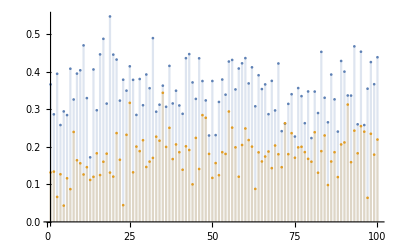

```mathematica
DiscretePlot[{stdodest[x],stdodold[x]},{x,1,100}]
```

```mathematica
For[i=1,i≤17,i++,
eiglist[i] = Eigenvalues[TestB[i]];
maxeig[i]=Max[eiglist[i]];
geomean[i]=GeometricMean[eiglist[i]]
]
```

Max::nord: Invalid comparison with 0.670034-0.0909419 ⅈ attempted.

Max::nord: Invalid comparison with 0.670034+0.0909419 ⅈ attempted.

Max::nord: Invalid comparison with 0.426689-0.0773903 ⅈ attempted.

General::stop: Further output of Max::nord will be suppressed during this calculation.